## Generatori di campioni casuali

## Inizializzazione

```mathematica
Clear["Global`*"];

n=5000;

(*Numeri casuali uniformi*)
u1=RandomVariate[UniformDistribution[],n];
u2=RandomVariate[UniformDistribution[],n];


(*Funzione di disegno grafici*)
creaPlot[dist_,campioni_,titolo_]:=
Module[{xmin,xmax},
xmin=Quantile[campioni,0.001];
xmax=Quantile[campioni,0.999];
Show[Histogram[campioni,100,"PDF",ChartStyle->Yellow],Plot[PDF[dist,x],
{x,xmin,xmax},
PlotStyle->{Red,Thick},
PlotRange->All],
PlotLabel->Style[titolo,14,Bold]]]
```

## Metodo dell’inversione

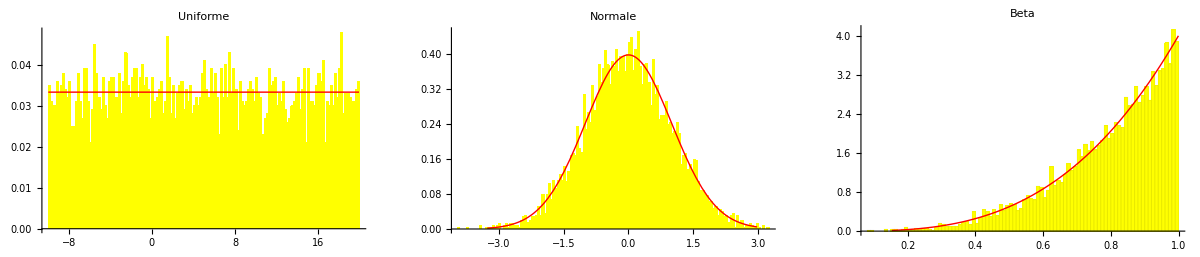

```mathematica
(*Distribuzioni scelte*)
titoli={"Uniforme","Normale","Beta"};
dist={UniformDistribution[{-10,20}],NormalDistribution[0,1],BetaDistribution[4,1]};

(*Trovo le CDF inverse*)
campioni=InverseCDF[#,u1]&/@dist;

(*Grafici*)
GraphicsGrid[{MapThread[creaPlot,{dist,campioni,titoli}]},ImageSize->Full]
```

## Trasformazione di Box-Muller

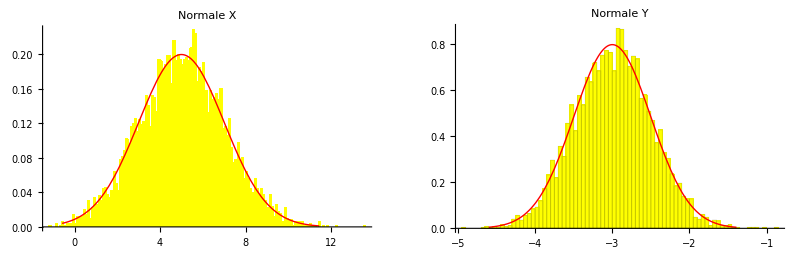

```mathematica
(*Formule*)
Z1=Sqrt[-2 Log[u1]] Cos[2 Pi u2];
Z2=Sqrt[-2 Log[u1]] Sin[2 Pi u2];

(*1) N(5,4)*)
mu1=5;
sigma1=2;

(*1) N(-3,0.25)*)
mu2=-3;
sigma2=0.5;

(*Trasformazione*)
X=mu1+sigma1 Z1;
Y=mu2+sigma2 Z2;

(*Grafici*)
GraphicsGrid[{{creaPlot[NormalDistribution[mu1,sigma1],X,"Normale X"],
creaPlot[NormalDistribution[mu2,sigma2],Y,"Normale Y"]}},ImageSize->Full]
```

## Metodo accettazione/rifiuto

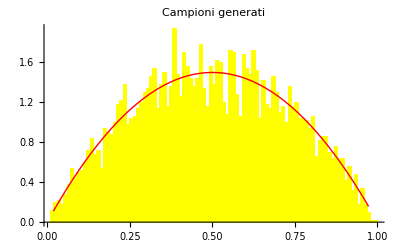

```mathematica
(*Densità obiettivo Beta(2,2)*)
f[x_]:=PDF[BetaDistribution[2,2],x];

(*Densità proposta U(0,1)*)
g[x_]:=PDF[UniformDistribution[{0,1}],x];

(*Costante tale che f(x)<=M g(x)*)
M=3/2;

campioni={};

(*Genera campioni finché non ne vengono accettati n*)
While[Length[campioni]<n,y=RandomVariate[UniformDistribution[{0,1}]];
u=RandomReal[];
If[u<=f[y]/(M g[y]),AppendTo[campioni,y]];];

(*Grafici*)
GraphicsRow[{Plot[{f[x],g[x],M g[x]},{x,0,1},PlotStyle->{{Red,Thick},{Blue,Thick},{Darker[Green],Dashed,Thick}},PlotLegends->{"f(x)","g(x)","Mg(x)"},PlotLabel->"Densità"],creaPlot[BetaDistribution[2,2],campioni,"Campioni generati"]},ImageSize->Full]
```